```mathematica
FSize1=30;
FSize2=24;
FontUse="Times";
```

```mathematica
SetDirectory[NotebookDirectory[]<>"..\\"<>"output"]
rvout = Import["rvout.dat","Table"];
sizeout= Import["sizeout.dat","Table"];
(*sizeout2= Import["buffout.dat","Table"];*)
```

D:\Users\StevenMoore\Projects\MMUVP_ECS_3_0\output

```mathematica
rvtest1= Table[{rvout[[i,3]],rvout[[i,2]]},{i,1,Length[rvout]}];
```

```mathematica
(*rvtest={{0,0}}
Do[
rvtest=Join[rvtest,{{Abs[rvout[[i,1]]-rvout[[i-1,1]]]*100+rvtest[[-1,1]],rvout[[i,2]]}}]
,{i,2,Length[rvout]}];*)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"..\\"<>"input\\experiment"];
exp= Import["exp_grain_size_1_6mkm.txt","Table"];
exp2= Import["exp_grain_size_40mkm.txt","Table"];
```

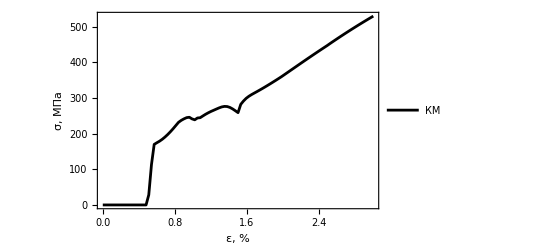

```mathematica
Img=ListLinePlot[{rvtest1} ,PlotRange-> {{0,All},{0,All}},Axes->True,Frame->True,FrameLabel->{Style["ε, %",FSize1, FontFamily->"Times"],Style["σ, МПа",FSize1, FontFamily->"Times"]},PlotLegends->Placed[{"КМ","Эксп. 40мкм"},Above], PlotStyle->{{Black,Thick},{Green,Thick},{Blue,Thick}}, LabelStyle->{FSize1, FontFamily->"Times"},AxesStyle->Directive[FSize2, FontFamily->"Times"],ImageSize->Scaled[.4]]
```

```mathematica
sizetest1= Table[{sizeout[[i,2]], sizeout[[i,1]]*10^6},{i,Length[sizeout]}]
```

{{0.03,200.},{0.06,200.},{0.09,200.},{0.12,200.},{0.15,200.},{0.18,200.},{0.21,200.},{0.24,200.},{0.27,200.},{0.3,200.},{0.33,200.},{0.36,200.},{0.39,200.},{0.42,200.},{0.45,200.},{0.48,200.},{0.51,200.},{0.54,200.},{0.57,200.},{0.6,200.},{0.63,200.},{0.66,200.},{0.69,200.},{0.72,200.},{0.75,200.},{0.78,200.},{0.81,199.99},{0.84,199.97},{0.87,199.9},{0.9,199.67},{0.93,198.84},{0.96,196.23},{0.99,189.61},{1.02,176.53},{1.05,156.86},{1.08,134.8},{1.11,114.91},{1.14,99.105},{1.17,87.387},{1.2,79.316},{1.23,74.446},{1.26,72.409},{1.29,72.847},{1.32,75.352},{1.35,79.477},{1.38,84.793},{1.41,91.001},{1.44,97.956},{1.47,105.6},{1.5,113.92},{1.53,122.94},{1.56,132.74},{1.59,143.38},{1.62,154.9},{1.65,167.34},{1.68,180.76},{1.71,195.18},{1.74,210.64},{1.77,227.17},{1.8,244.8},{1.83,263.57},{1.86,283.5},{1.89,304.63},{1.92,326.98},{1.95,350.58},{1.98,375.46},{2.01,401.65},{2.04,429.23},{2.07,458.26},{2.1,488.76},{2.13,520.76},{2.16,554.29},{2.19,589.38},{2.22,626.06},{2.25,664.35},{2.28,704.29},{2.31,745.89},{2.34,789.19},{2.37,834.21},{2.4,880.97},{2.43,929.51},{2.46,979.85},{2.49,1032.},{2.52,1086.},{2.55,1142.},{2.58,1200.},{2.61,1260.},{2.64,1322.1},{2.67,1386.2},{2.7,1452.5},{2.73,1520.8},{2.76,1591.3},{2.79,1664.},{2.82,1738.9},{2.85,1816.},{2.88,1895.4},{2.91,1977.},{2.94,2060.9},{2.97,2147.2},{3,2235.7}}

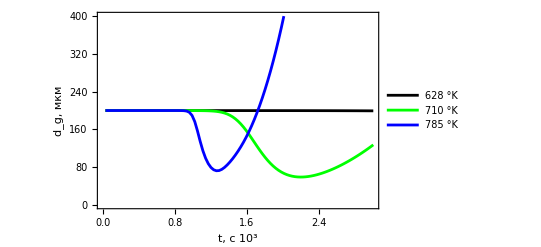

```mathematica
Img=ListLinePlot[{sizetest2,sizetest,sizetest1} ,PlotRange-> {{0,All},{0,400}},Axes->True,Frame->True,FrameLabel->{Style["t, c 10^3",FSize1, FontFamily->"Times"],Style["d_g, мкм",FSize1, FontFamily->"Times"]},PlotLegends->Placed[{"628 °K","710 °K","785 °K"},Above], PlotStyle->{{Black,Thick},{Green,Thick},{Blue,Thick}}, LabelStyle->{FSize1, FontFamily->"Times"},AxesStyle->Directive[FSize2, FontFamily->"Times"],ImageSize->Scaled[.4]]
```

```mathematica
(*Export["D:\\Users\\StevenMoore\\Downloads\\Отчет лаборатория\\A.jpg", Img]*)
```

```mathematica
600+273
%*0.7
```

873

611.1